```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
data=Import["Samples.xls"];
```

```mathematica
samples=Map[Drop[#,1]&,Transpose[data[[1]]]];
```

```mathematica
u=UniformDistribution[{0,20}];
b=BinomialDistribution[50,.6];
p=PoissonDistribution[10];
```

```mathematica
s1=Show[SmoothHistogram[samples[[1]],Automatic,PlotStyle->Red],DiscretePlot[PDF[b,x],{x,0,50},ExtentSize->.9],PlotLabel->Style["Sample One With Binomial PDF",8]];
```

```mathematica
s2=Show[SmoothHistogram[samples[[2]],Automatic,PlotStyle->Red],DiscretePlot[PDF[UniformDistribution[{0,20}],x],{x,0,20},ExtentSize->.9],PlotLabel->Style["Sample Two With Uniform PDF",8]];
```

```mathematica
s3=Show[SmoothHistogram[samples[[3]],Automatic,PlotStyle->Red],DiscretePlot[PDF[p,x],{x,0,50},ExtentSize->.9],PlotLabel->Style["Sample Three With Poisson PDF",8]];
```

```mathematica
s4=Show[Plot[PDF[SmoothKernelDistribution[samples[[4]],.5],x],{x,4,14},PlotStyle->Red,PlotRange->{0,.4}],DiscretePlot[PDF[p,x],{x,0,50},ExtentSize->.9],PlotLabel->Style["Sample Four With Poisson PDF",8]];
```

```mathematica
s5=Show[SmoothHistogram[samples[[5]],Automatic,PlotStyle->Red],DiscretePlot[PDF[p,x],{x,0,50},ExtentSize->.9],PlotLabel->Style["Sample Five With Poisson PDF",8]];
```

```mathematica
s6=Show[SmoothHistogram[samples[[6]],Automatic,PlotStyle->Red],DiscretePlot[PDF[UniformDistribution[{0,20}],x],{x,0,20},ExtentSize->.9],PlotLabel->Style["Sample Six With Uniform PDF",8]];
```

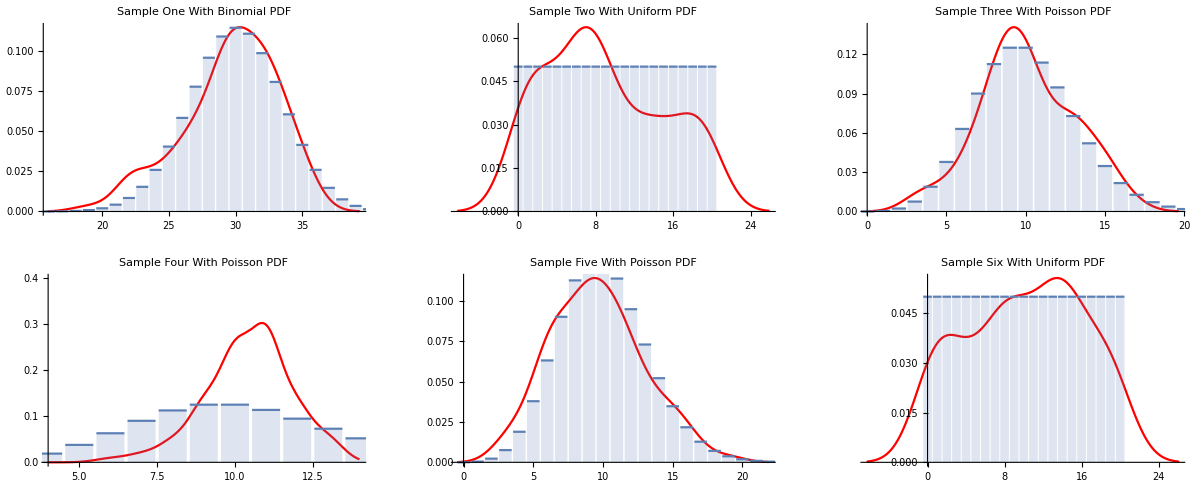

```mathematica
s11=GraphicsGrid[{{s1,s2,s3},{s4,s5,s6}},ImageSize->Full]
```

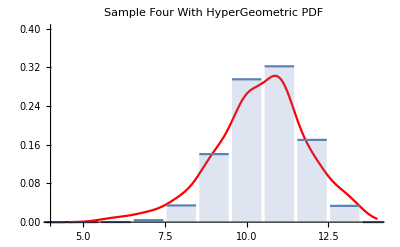

```mathematica
s4=Show[Plot[PDF[SmoothKernelDistribution[samples[[4]],.5],x],{x,4,14},PlotStyle->Red,PlotRange->{0,.4}],DiscretePlot[PDF[HypergeometricDistribution[13,30,37],x],{x,0,14},ExtentSize->.9,PlotRange->{0,.4}],PlotLabel->Style["Sample Four With HyperGeometric PDF",8]]
```

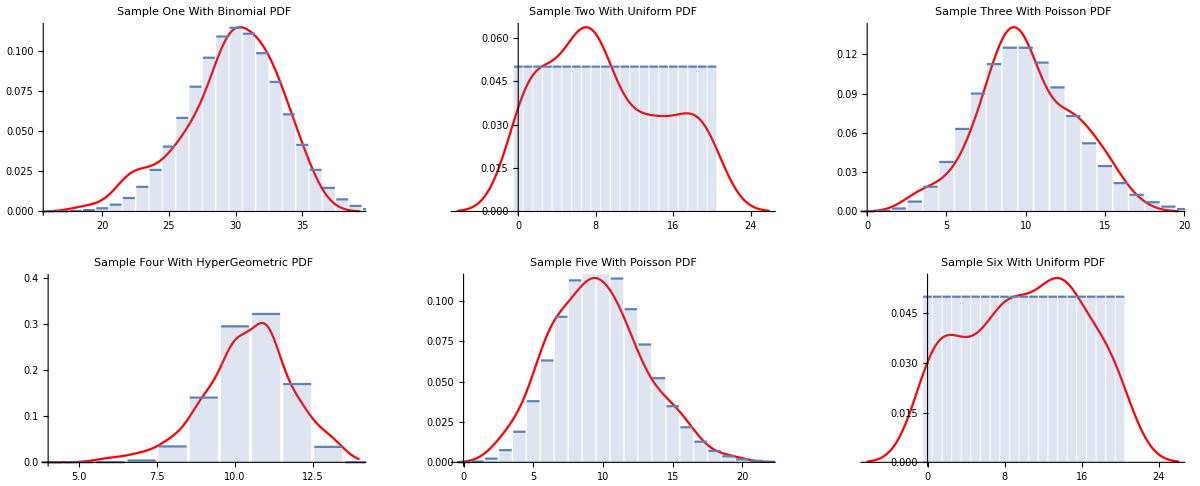

```mathematica
s12=GraphicsGrid[{{s1,s2,s3},{s4,s5,s6}},ImageSize->Full]
```

```mathematica
rando[n_]:=RandomInteger[{0,20},n]
```

```mathematica
g1:=rando[100];
```

```mathematica
g2:=RandomVariate[b,100];
```

```mathematica
g3:=RandomVariate[p,100];
```

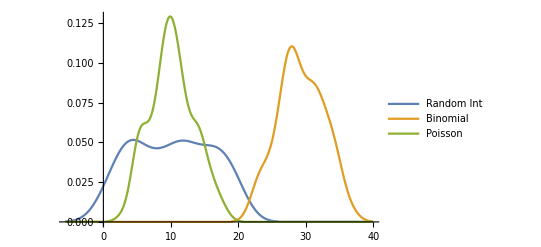

```mathematica
SmoothHistogram[{g1,g2,g3},PlotLegends->{"Random Int","Binomial","Poisson"}]
```